```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"all", "zoo"}]]
```

/Users/jonaprieto/Imputation/databases/all/zoo

```mathematica
data1=Import["RINS-0.05.csv"][[5]] //Take[#, 15]&
```

{0.851852,0.814815,0.814815,0.851852,0.876543,0.851852,0.814815,0.851852,0.876543,0.802469,0.82716,0.790123,0.82716,0.82716,0.777778}

```mathematica
msgs = {"Samples of Zoo dataset","Accuracy Ratio (%)"}
rango = {{1,15},{0.75,0.9}};
size = {800,500};
```

{Samples of Zoo dataset,Accuracy Ratio (%)}

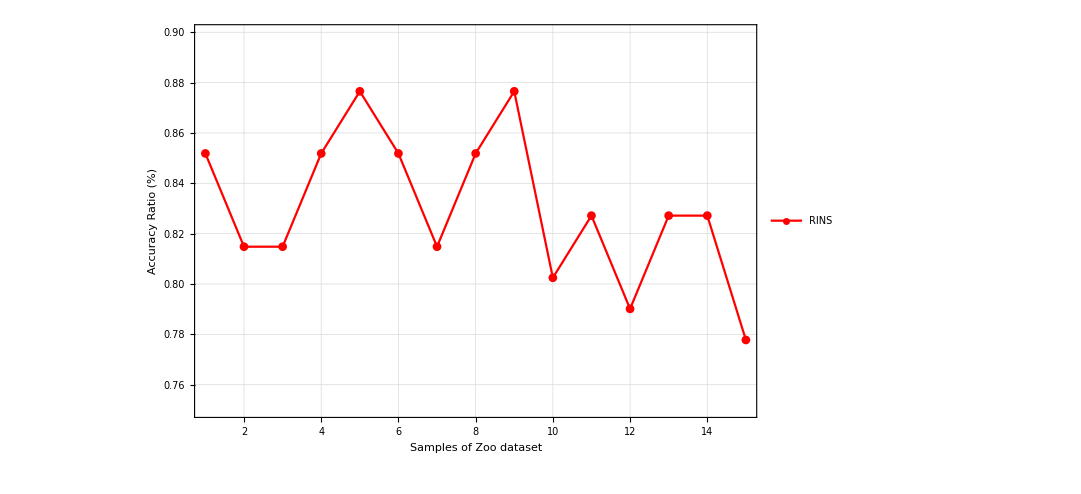

```mathematica
fig1= ListPlot[data1, 
				Joined -> True, 
				PlotStyle -> {Red}, 
				PlotLegends -> {"RINS"},
				GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.78],Dashed],
				PlotRange->rango,
				ImageSize->size,
				AxesLabel->msgs ,
				Frame-> True,
				FrameLabel->msgs ,
				PlotMarkers->Automatic, LabelStyle->Directive[Bold,Medium,28], AxesStyle->Black]
```

```mathematica
data2=Import["ROUSTIDA-0.05.csv"][[5]]//Take[#, 15]&
```

{0.82716,0.814815,0.82716,0.851852,0.864198,0.839506,0.802469,0.839506,0.839506,0.777778,0.82716,0.790123,0.790123,0.802469,0.790123}

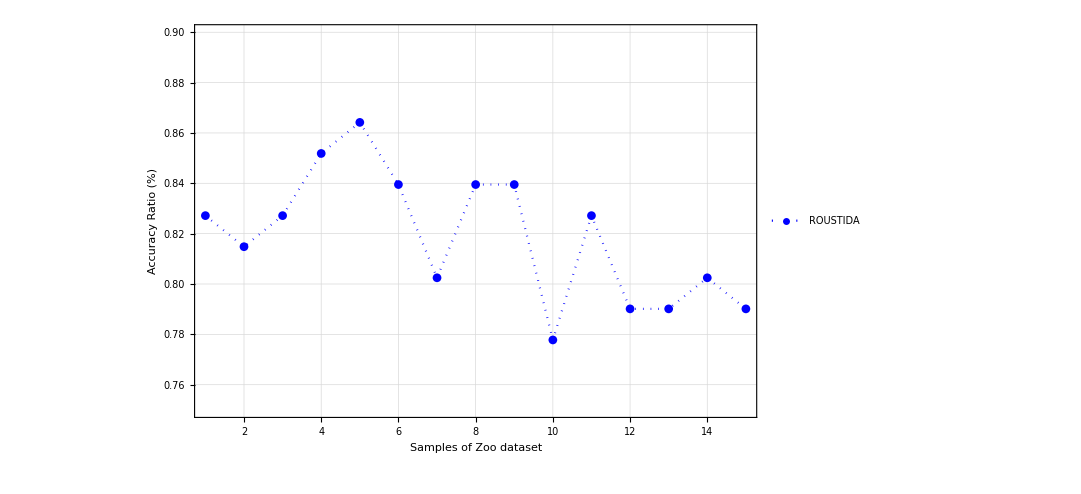

```mathematica
fig2= ListPlot[data2, 
				Joined -> True, 
				PlotStyle -> {Blue,Dotted}, 
				PlotLegends -> {"ROUSTIDA"},
				GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.78],Dashed],
				PlotRange->rango,
				ImageSize->size,
				AxesLabel->msgs ,
				Frame-> True,
				FrameLabel->msgs ,
				PlotMarkers->Automatic, LabelStyle->Directive[Bold,Medium,18]]
```

```mathematica
data3=Import["VTRIDA-0.05.csv"][[5]]//Take[#, 15]&
```

{0.839506,0.814815,0.814815,0.864198,0.864198,0.864198,0.765432,0.82716,0.864198,0.777778,0.802469,0.802469,0.802469,0.814815,0.777778}

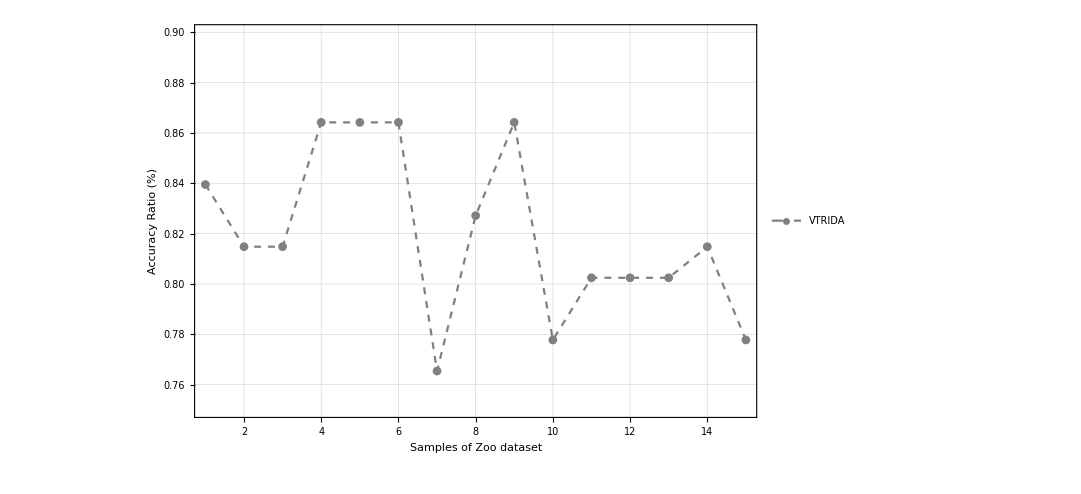

```mathematica
fig3= ListPlot[data3, 
				Joined -> True, 
				PlotStyle -> {Gray,Dashed}, 
				PlotLegends -> {"VTRIDA"},
				GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.78],Dashed],
				PlotRange->rango,
				ImageSize->size,
				AxesLabel->msgs ,
				Frame-> True,
				FrameLabel->msgs ,
				PlotMarkers->Automatic, LabelStyle->Directive[Bold,Medium,18]]
```

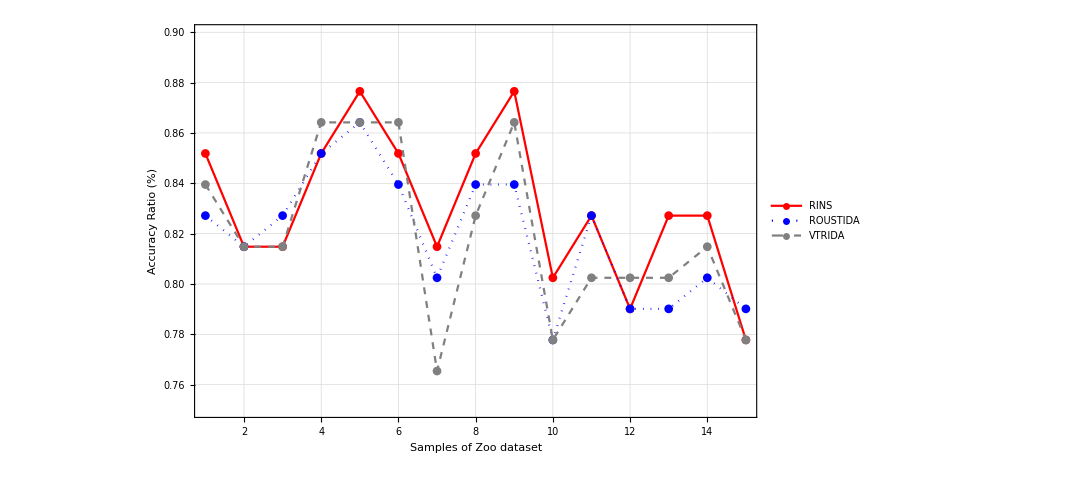

```mathematica
Figure1=Show[{fig1,fig2,fig3}]
```

```mathematica
Export["/Users/jonaprieto/imputation-article/figs/zoo005.eps",Figure1]
```

/Users/jonaprieto/imputation-article/figs/zoo005.eps

```mathematica
Table[ If[data1[[i]] ≥ data2[[i]], 1, Nothing], {i, 1, 15}]//Total
```

13

```mathematica
Table[ If[data1[[i]] >= data3[[i]], 1, Nothing], {i, 1, 15}]//Total
```

12

```mathematica
(13/15)* 100 // N
```

86.6667

```mathematica
LabelS
```